Computation of the Cramer-Rao bound (van Trees inequality) for the joint estimation of a phase and four visibilities.

2x2 Fisher information matrix for a phase and a visibility:

Probabilities for the Type-0 measurement

```mathematica
p1z=(1+V*Cos[s*θ])/2
```

1/2 (1+V Cos[s θ])

```mathematica
p2z=(1-V*Cos[s*θ])/2
```

1/2 (1-V Cos[s θ])

Fisher information entries for the Type-0 measurement

```mathematica
F11z =FullSimplify[(FullSimplify[D[Log[p1z], θ]])*(FullSimplify[D[Log[p1z], θ]])*p1z+(FullSimplify[D[Log[p2z], θ]])*(FullSimplify[D[Log[p2z], θ]])*p2z]
```

-(s^2 V^2 Sin[s θ]^2)/(-1+V^2 Cos[s θ]^2)

```mathematica
F12z =FullSimplify[(FullSimplify[D[Log[p1z], θ]])*(FullSimplify[D[Log[p1z], V]])*p1z+(FullSimplify[D[Log[p2z], θ]])*(FullSimplify[D[Log[p2z], V]])*p2z]
```

(s V Tan[s θ])/(V^2-Sec[s θ]^2)

```mathematica
F22z =FullSimplify[(FullSimplify[D[Log[p1z], V]])*(FullSimplify[D[Log[p1z], V]])*p1z+(FullSimplify[D[Log[p2z], V]])*(FullSimplify[D[Log[p2z], V]])*p2z]
```

1/(-V^2+Sec[s θ]^2)

Fisher information matrix

```mathematica
Fz= {{F11z, F12z}, {F12z, F22z}}
```

{{-(s^2 V^2 Sin[s θ]^2)/(-1+V^2 Cos[s θ]^2),(s V Tan[s θ])/(V^2-Sec[s θ]^2)},{(s V Tan[s θ])/(V^2-Sec[s θ]^2),1/(-V^2+Sec[s θ]^2)}}

Probabilities of the outcomes for the Type-+ measurements

```mathematica
p1p=(1+V*Sin[s*θ])/2
```

1/2 (1+V Sin[s θ])

```mathematica
p2p=(1-V*Sin[s*θ])/2
```

1/2 (1-V Sin[s θ])

```mathematica
F11p =FullSimplify[(FullSimplify[D[Log[p1p], θ]])*(FullSimplify[D[Log[p1p], θ]])*p1p+(FullSimplify[D[Log[p2p], θ]])*(FullSimplify[D[Log[p2p], θ]])*p2p]
```

-(s^2 V^2 Cos[s θ]^2)/(-1+V^2 Sin[s θ]^2)

```mathematica
F12p =FullSimplify[(FullSimplify[D[Log[p1p], θ]])*(FullSimplify[D[Log[p1p], V]])*p1p+(FullSimplify[D[Log[p2p], θ]])*(FullSimplify[D[Log[p2p], V]])*p2p]
```

-(s V Cot[s θ])/(V^2-Csc[s θ]^2)

```mathematica
F22p =FullSimplify[(FullSimplify[D[Log[p1p], V]])*(FullSimplify[D[Log[p1p], V]])*p1p+(FullSimplify[D[Log[p2p], V]])*(FullSimplify[D[Log[p2p], V]])*p2p]
```

1/(-V^2+Csc[s θ]^2)

Fisher information matrix for the Type-+ measurement

```mathematica
Fp= {{F11p, F12p}, {F12p, F22p}}
```

{{-(s^2 V^2 Cos[s θ]^2)/(-1+V^2 Sin[s θ]^2),-(s V Cot[s θ])/(V^2-Csc[s θ]^2)},{-(s V Cot[s θ])/(V^2-Csc[s θ]^2),1/(-V^2+Csc[s θ]^2)}}

Total FI for the two measurements Type-0 and Type-+

```mathematica
F = FullSimplify[Fp+Fz]
```

{{(2 s^2 V^2 (-4+3 V^2+V^2 Cos[4 s θ]))/(-8+8 V^2-V^4+V^4 Cos[4 s θ]),-(2 s V^3 Cot[2 s θ])/((V^2-Csc[s θ]^2) (V^2-Sec[s θ]^2))},{-(2 s V^3 Cot[2 s θ])/((V^2-Csc[s θ]^2) (V^2-Sec[s θ]^2)),1/(-V^2+Csc[s θ]^2)+1/(-V^2+Sec[s θ]^2)}}

```mathematica
MatrixForm[F]
```

((2 s^2 V^2 (-4+3 V^2+V^2 Cos[4 s θ]))/(-8+8 V^2-V^4+V^4 Cos[4 s θ]) | -(2 s V^3 Cot[2 s θ])/((V^2-Csc[s θ]^2) (V^2-Sec[s θ]^2))
-(2 s V^3 Cot[2 s θ])/((V^2-Csc[s θ]^2) (V^2-Sec[s θ]^2)) | 1/(-V^2+Csc[s θ]^2)+1/(-V^2+Sec[s θ]^2))

```mathematica
FullSimplify[Inverse[F]]
```

{{(4-V^2+V^2 Cos[4 s θ])/(4 s^2 V^2),(V Sin[4 s θ])/(4 s)},{(V Sin[4 s θ])/(4 s),1/4 (4-3 V^2-V^2 Cos[4 s θ])}}

Mean value of the CR bound for the variance if the phase is perfectly known.

The CR bound on the visibility in case the phase is known and in case the phase is unknown are very similar

```mathematica
Manipulate[Plot[{(1/(-V^2+Csc[s θ]^2)+1/(-V^2+Sec[s θ]^2))^(-1), 1/4 (4-3 V^2-V^2 Cos[4 s θ])}, {V, 0, 1}], {s, 1, 100}, {θ, 0, Pi}]
```

```mathematica
FullSimplify[(1/(-V^2+Csc[s θ]^2)+1/(-V^2+Sec[s θ]^2))^(-1)]
```

1/(1/(-V^2+Csc[s θ]^2)+1/(-V^2+Sec[s θ]^2))

Global approach to the CR bound in which we write a single Fisher Information matrix (5x5) for all the parameters.

```mathematica
i1 = F/.{s-> s1, V-> V1};
```

```mathematica
i2 = F/.{s-> s2, V-> V2};
```

```mathematica
i3 = F/.{s-> s3, V-> V3};
```

```mathematica
i4 = F/.{s-> s4, V-> V4};
```

```mathematica
I1 = FullSimplify[{{i1[[1, 1]], i1[[1, 2]], 0, 0, 0}, {i1[[2, 1]], i1[[2, 2]], 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}}]
```

{{(2 s1^2 V1^2 (-4+3 V1^2+V1^2 Cos[4 s1 θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 s1 θ]),-(2 s1 V1^3 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)),0,0,0},{-(2 s1 V1^3 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)),1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2),0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
MatrixForm[I1]
```

((2 s1^2 V1^2 (-4+3 V1^2+V1^2 Cos[4 s1 θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 s1 θ]) | -(2 s1 V1^3 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)) | 0 | 0 | 0
-(2 s1 V1^3 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)) | 1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
I2 = FullSimplify[{{i2[[1, 1]], 0, i2[[1, 2]], 0, 0}, {0, 0, 0, 0, 0},{i2[[2, 1]], 0, i2[[2, 2]], 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}}]
```

{{(2 s2^2 V2^2 (-4+3 V2^2+V2^2 Cos[4 s2 θ]))/(-8+8 V2^2-V2^4+V2^4 Cos[4 s2 θ]),0,-(2 s2 V2^3 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)),0,0},{0,0,0,0,0},{-(2 s2 V2^3 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)),0,1/(-V2^2+Csc[s2 θ]^2)+1/(-V2^2+Sec[s2 θ]^2),0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
MatrixForm[I2]
```

((2 s2^2 V2^2 (-4+3 V2^2+V2^2 Cos[4 s2 θ]))/(-8+8 V2^2-V2^4+V2^4 Cos[4 s2 θ]) | 0 | -(2 s2 V2^3 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)) | 0 | 0
0 | 0 | 0 | 0 | 0
-(2 s2 V2^3 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)) | 0 | 1/(-V2^2+Csc[s2 θ]^2)+1/(-V2^2+Sec[s2 θ]^2) | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
I3= FullSimplify[{{i3[[1, 1]], 0, 0, i3[[1, 2]], 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0},{i3[[2, 1]], 0, 0, i3[[2, 2]], 0}, {0, 0, 0, 0, 0}}]
```

{{(2 s3^2 V3^2 (-4+3 V3^2+V3^2 Cos[4 s3 θ]))/(-8+8 V3^2-V3^4+V3^4 Cos[4 s3 θ]),0,0,-(2 s3 V3^3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)),0},{0,0,0,0,0},{0,0,0,0,0},{-(2 s3 V3^3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)),0,0,1/(-V3^2+Csc[s3 θ]^2)+1/(-V3^2+Sec[s3 θ]^2),0},{0,0,0,0,0}}

```mathematica
MatrixForm[I3]
```

((2 s3^2 V3^2 (-4+3 V3^2+V3^2 Cos[4 s3 θ]))/(-8+8 V3^2-V3^4+V3^4 Cos[4 s3 θ]) | 0 | 0 | -(2 s3 V3^3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)) | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-(2 s3 V3^3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)) | 0 | 0 | 1/(-V3^2+Csc[s3 θ]^2)+1/(-V3^2+Sec[s3 θ]^2) | 0
0 | 0 | 0 | 0 | 0)

```mathematica
I4= FullSimplify[{{i4[[1, 1]], 0, 0, 0, i4[[1, 2]]}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {i4[[2, 1]], 0, 0, 0, i4[[2, 2]]}}]
```

{{(2 s4^2 V4^2 (-4+3 V4^2+V4^2 Cos[4 s4 θ]))/(-8+8 V4^2-V4^4+V4^4 Cos[4 s4 θ]),0,0,0,-(2 s4 V4^3 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2))},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{-(2 s4 V4^3 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2)),0,0,0,1/(-V4^2+Csc[s4 θ]^2)+1/(-V4^2+Sec[s4 θ]^2)}}

```mathematica
MatrixForm[I4]
```

((2 s4^2 V4^2 (-4+3 V4^2+V4^2 Cos[4 s4 θ]))/(-8+8 V4^2-V4^4+V4^4 Cos[4 s4 θ]) | 0 | 0 | 0 | -(2 s4 V4^3 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2))
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-(2 s4 V4^3 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2)) | 0 | 0 | 0 | 1/(-V4^2+Csc[s4 θ]^2)+1/(-V4^2+Sec[s4 θ]^2))

```mathematica
Itot =ν1*I1+ν2*I2+ν3*I3+ν4*I4
```

{{(2 s1^2 V1^2 ν1 (-4+3 V1^2+V1^2 Cos[4 s1 θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 s1 θ])+(2 s2^2 V2^2 ν2 (-4+3 V2^2+V2^2 Cos[4 s2 θ]))/(-8+8 V2^2-V2^4+V2^4 Cos[4 s2 θ])+(2 s3^2 V3^2 ν3 (-4+3 V3^2+V3^2 Cos[4 s3 θ]))/(-8+8 V3^2-V3^4+V3^4 Cos[4 s3 θ])+(2 s4^2 V4^2 ν4 (-4+3 V4^2+V4^2 Cos[4 s4 θ]))/(-8+8 V4^2-V4^4+V4^4 Cos[4 s4 θ]),-(2 s1 V1^3 ν1 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)),-(2 s2 V2^3 ν2 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)),-(2 s3 V3^3 ν3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)),-(2 s4 V4^3 ν4 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2))},{-(2 s1 V1^3 ν1 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)),ν1 (1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2)),0,0,0},{-(2 s2 V2^3 ν2 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)),0,ν2 (1/(-V2^2+Csc[s2 θ]^2)+1/(-V2^2+Sec[s2 θ]^2)),0,0},{-(2 s3 V3^3 ν3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)),0,0,ν3 (1/(-V3^2+Csc[s3 θ]^2)+1/(-V3^2+Sec[s3 θ]^2)),0},{-(2 s4 V4^3 ν4 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2)),0,0,0,ν4 (1/(-V4^2+Csc[s4 θ]^2)+1/(-V4^2+Sec[s4 θ]^2))}}

```mathematica
MatrixForm[Itot]
```

((2 s1^2 V1^2 ν1 (-4+3 V1^2+V1^2 Cos[4 s1 θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 s1 θ])+(2 s2^2 V2^2 ν2 (-4+3 V2^2+V2^2 Cos[4 s2 θ]))/(-8+8 V2^2-V2^4+V2^4 Cos[4 s2 θ])+(2 s3^2 V3^2 ν3 (-4+3 V3^2+V3^2 Cos[4 s3 θ]))/(-8+8 V3^2-V3^4+V3^4 Cos[4 s3 θ])+(2 s4^2 V4^2 ν4 (-4+3 V4^2+V4^2 Cos[4 s4 θ]))/(-8+8 V4^2-V4^4+V4^4 Cos[4 s4 θ]) | -(2 s1 V1^3 ν1 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)) | -(2 s2 V2^3 ν2 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)) | -(2 s3 V3^3 ν3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)) | -(2 s4 V4^3 ν4 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2))
-(2 s1 V1^3 ν1 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)) | ν1 (1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2)) | 0 | 0 | 0
-(2 s2 V2^3 ν2 Cot[2 s2 θ])/((V2^2-Csc[s2 θ]^2) (V2^2-Sec[s2 θ]^2)) | 0 | ν2 (1/(-V2^2+Csc[s2 θ]^2)+1/(-V2^2+Sec[s2 θ]^2)) | 0 | 0
-(2 s3 V3^3 ν3 Cot[2 s3 θ])/((V3^2-Csc[s3 θ]^2) (V3^2-Sec[s3 θ]^2)) | 0 | 0 | ν3 (1/(-V3^2+Csc[s3 θ]^2)+1/(-V3^2+Sec[s3 θ]^2)) | 0
-(2 s4 V4^3 ν4 Cot[2 s4 θ])/((V4^2-Csc[s4 θ]^2) (V4^2-Sec[s4 θ]^2)) | 0 | 0 | 0 | ν4 (1/(-V4^2+Csc[s4 θ]^2)+1/(-V4^2+Sec[s4 θ]^2)))

A uniform prior gives zero Fisher information

Non diagonal terms of the Fisher information matrix have null mean value

```mathematica
Integrate[-(2 s1 V1^3 ν1 Cot[2 s1 θ])/((V1^2-Csc[s1 θ]^2) (V1^2-Sec[s1 θ]^2)), {θ, 0, 2*Pi}]
```

```mathematica
ConditionalExpression[-(ν1 (-Log[4-4 V1^2]+Log[4-4 V1^2+V1^4 Sin[4 π s1]^2]))/(2 V1), 8 V1^2+V1^4 Cos[8 π s1]≠8+V1^4&&(Re[((-1+V1^2) Csc[4 π s1]^2)/V1^4]<0||4 Re[((-1+V1^2) Csc[4 π s1]^2)/V1^4]>1||((-1+V1^2) Csc[4 π s1]^2)/V1^4∉Reals)&&(Re[((-8+8 V1^2-V1^4+V1^4 Cos[8 π s1]) Csc[4 π s1]^2)/V1^4]<-2||Re[((-8+8 V1^2-V1^4+V1^4 Cos[8 π s1]) Csc[4 π s1]^2)/V1^4]>0||((-8+8 V1^2-V1^4+V1^4 Cos[8 π s1]) Csc[4 π s1]^2)/V1^4∉Reals)]
```

The condition is true for V in (0, 1), at the extrema V=0 and V=1 the condition is false

```mathematica
Integrate[(2 s1^2 V1^2 ν1 (-4+3 V1^2+V1^2 Cos[4 s1 θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 s1 θ]), θ]
```

2 s1^2 V1^2 ν1 (θ/V1^2+(√(-1+V1^2) ArcTanh[((-2+V1^2) Tan[2 s1 θ])/(2 √(-1+V1^2))])/(2 s1 V1^2))

```mathematica
Integrate[(2 s1^2 V1^2 ν1 (-4+3 V1^2+V1^2 Cos[4 s1 θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 s1 θ]), θ]
```

2 s1^2 V1^2 ν1 (θ/V1^2+(√(-1+V1^2) ArcTanh[((-2+V1^2) Tan[2 s1 θ])/(2 √(-1+V1^2))])/(2 s1 V1^2))

```mathematica
Manipulate[Plot[2 s1^2 V1^2 ν1 (θ/V1^2+(√(-1+V1^2) ArcTanh[((-2+V1^2) Tan[2 s1 θ])/(2 √(-1+V1^2))])/(2 s1 V1^2)), {θ, 0, 2*Pi}], {ν1, 1, 100}, {V1, 0.001, 1}, {s1, 1, 51}]
```

The computation for a generic s is reduced to the computation or s1 = 1, we should remember to multiply for s1^2.

```mathematica
Integrate[(2 V1^2 ν1 (-4+3 V1^2+V1^2 Cos[4 * θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 * θ]), {θ, 0, Pi/4}]
```

```mathematica
ConditionalExpression[1/2 ν1 (π+√(-1+V1^2) (-Log[(2-V1^2)/(√(-1+V1^2))]+Log[(-2+V1^2)/(√(-1+V1^2))])), Im[ArcCos[1+8/V1^4-8/V1^2]]≠0||Re[ArcCos[1+8/V1^4-8/V1^2]]>π||Re[ArcCos[1+8/V1^4-8/V1^2]]<0]
```

```mathematica
FullSimplify[1/2*ν1*(π+√(-1+V1^2)*(-Log[Abs[(2-V1^2)/(√(-1+V1^2))]]-I Arg[(2-V1^2)/(√(-1+V1^2))]+Log[Abs[(-2+V1^2)/(√(-1+V1^2))]]+I Arg[(-2+V1^2)/(√(-1+V1^2))]))]
```

1/2 ν1 (π-ⅈ √(-1+V1^2) (Arg[(2-V1^2)/(√(-1+V1^2))]-Arg[(-2+V1^2)/(√(-1+V1^2))]))

The difference of arguments between z and -z can be Pi or -Pi, in this case only -Pi makes sense.

```mathematica
1/2*ν1*(Pi-Sqrt[1-V1^2]*Pi)
```

1/2 (π-π √(1-V1^2)) ν1

Mean value

```mathematica
FullSimplify[(1/2 (π-π √(1-V1^2)) ν1)/(2*π)]
```

-1/4 (-1+√(1-V1^2)) ν1

This value refers only to an integration in the interval [0, Pi/4]. We need to multiply for 8.

```mathematica
Manipulate[Plot[(2 V1^2 ν1 (-4+3 V1^2+V1^2 Cos[4 * θ]))/(-8+8 V1^2-V1^4+V1^4 Cos[4 * θ]), {θ, 0, 2*Pi}, PlotRange->{{0, 2*Pi}, {0, 100}}], {ν1, 1, 100}, {V1, 0.001, 1}, {s1, 1, 51}]
```

```mathematica
FullSimplify[-1/4 (-1+√(1-V1^2)) ν1*8]
```

-2 (-1+√(1-V1^2)) ν1

Computation for s2, s3, and s4:

```mathematica
2*s2^2*ν2*(1-Sqrt[1-V2^2])
```

2 s2^2 (1-√(1-V2^2)) ν2

Diagonal term of the FI matrix referring to the unknown visibilities

```mathematica
Integrate[ν1 (1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2)),{θ,0,Pi/4}]
```

ConditionalExpression[-(ν1 (π s1 √(-1+V1^2)+2 ArcTanh[Tan[(π s1)/4]/(√(-1+V1^2))]-2 (ArcTanh[√(-1+V1^2) Tan[(π s1)/4]]-Log[-(√(-1+V1^2))/s1]+Log[(√(-1+V1^2))/s1])))/(2 s1 V1^2 √(-1+V1^2)), ]

```mathematica
Integrate[ν1 (1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2)),θ]
```

(ν1 (-2 s1 √(-1+V1^2) θ-ArcTanh[Tan[s1 θ]/(√(-1+V1^2))]+ArcTanh[√(-1+V1^2) Tan[s1 θ]]))/(s1 V1^2 √(-1+V1^2))

```mathematica
Manipulate[Plot[(ν1 (-2 s1 √(-1+V1^2) θ-ArcTanh[Tan[s1 θ]/(√(-1+V1^2))]+ArcTanh[√(-1+V1^2) Tan[s1 θ]]))/(s1 V1^2 √(-1+V1^2)), {θ, 0, 2*Pi}, PlotRange->{{0, 2*Pi}, {0, 2000}}], {ν1, 1, 100}, {V1, 0.001, 1}, {s1, 1, 51}]
```

```mathematica
Manipulate[Plot[ν1 (1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2)), {θ, 0, 2*Pi}, PlotRange->{{0, 2*Pi}, {0, 200}}], {ν1, 1, 100}, {V1, 0.001, 1}, {s1, 1, 51}]
```

```mathematica
Integrate[ν1 (1/(-V1^2+Csc[s1 θ]^2)+1/(-V1^2+Sec[s1 θ]^2)), θ]
```

(ν1 (-2 s1 √(-1+V1^2) θ-ArcTanh[Tan[s1 θ]/(√(-1+V1^2))]+ArcTanh[√(-1+V1^2) Tan[s1 θ]]))/(s1 V1^2 √(-1+V1^2))

```mathematica
(ν1 (-2 s1 √(-1+V1^2) θ-ArcTanh[Tan[s1 θ]/(√(-1+V1^2))]+ArcTanh[√(-1+V1^2) Tan[s1 θ]]))/(s1 V1^2 √(-1+V1^2))/.{θ-> Pi/(4*s1)}
```

(ν1 (-1/2 π √(-1+V1^2)-ArcTanh[1/(√(-1+V1^2))]+ArcTanh[√(-1+V1^2)]))/(s1 V1^2 √(-1+V1^2))

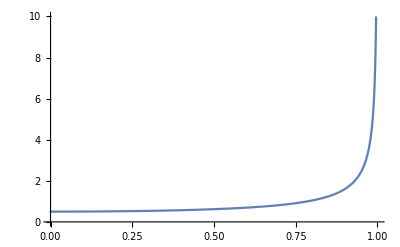

```mathematica
Plot[(1-Sqrt[1-V^2])/(V^2*Sqrt[1-V^2]), {V, 0,1}, PlotRange->{{0, 1}, {0, 10}}]
```

Substituting a logarithmic expression for the ArcTan we get the expression for the mean value of the Fisher Information for V

```mathematica
2*ν*(1-Sqrt[1-V^2])/(V^2*Sqrt[1-V^2])
```

(2 (1-√(1-V^2)) ν)/(V^2 √(1-V^2))